```mathematica
ClearAll["Global`*"]
```

```mathematica
Physical constants
```

```mathematica
sw = √0.23116;cw = √(1 - sw^2);
mZ = 91.1876; mW = 80.399;
(*mtpole = 173.1-0.7*2.5;*)

GF = 1.16637 10^-5;
v=1/(√(√2*GF));
mb=4.19;mc=1.27;ms=0.1;
α0=1/137.035999679;
ΔαhmZ=0.02758;
αmZ= α0/(1-0.03150-ΔαhmZ+0.00007);
αsmZ=0.1181+0.0011*(1);

Mpl=2.4*10^18;
mhpole=125.18+0.16*(0);

ye=2.8*10^-6;
yμ=5.9*10^-4;
yτ=1.0*10^-2;
yd=1.6*10^-5/2;
ys=3.1*10^-4/2;
yb=1.6*10^-2/2;
yu=7.4*10^-6/2;
yc=3.6*10^-3/2;
```

```mathematica
Runnnig of the standard model couplings
```

couplings model of Runnnig standard the

```mathematica
yt ,λ,g3: 3 loop for yt, λ, g3 while   2 loop for g1,g2
g1,g2 : 2 loop
```

```mathematica
(*Smoothed UnisStep. Without this, the ND solve it stuck around the UnisStep*)
(*SmoothUnitStep[x_]:=ArcTan[10x]/π+1/2;*)
(*loop counter*)
κ=1/(16*Pi^2);

(*numbers of flavors*)
nf=6;
ng=3;

z3=Zeta[3];

(*QCD colour factors*)
ca=3;
dR=3;
cf=4/3;
cr=1/2;


(*Beta function for top-Yukawa*)βyt[λ_,yt_,g3_,g2_,g1_]:=2*yt*(+κ*yt^2*(3/4+1/2*dR)+κ*g3^2*(-3*cf)+κ^2*λ^2*(3)+κ^2*yt^2*λ*(-6)+κ^2*yt^4*(3/4-9/4*dR)+κ^2*g3^2*yt^2*(6*cf+5/2*cf*dR)+κ^2*g3^4*(-3/2*cf^2-97/6*ca*cf+10/3*nf*cr*cf)+κ^3*λ^3*(-18)+κ^3*yt^2*λ^2*(285/8-45/4*dR)+κ^3*yt^4*λ*(63/2+45/2*dR)+κ^3*yt^6*(-345/32+107/32*dR+39/16*dR^2+9/4*z3+3/2*z3*dR)+κ^3*g3^2*yt^2*λ*(6*cf)+κ^3*g3^2*yt^4*(-57/2*cf-81/8*cf*dR)+κ^3*g3^4*yt^2*(471/16*cf^2-119/8*cf^2*dR+25*cr*cf+717/16*ca*cf+77/4*ca*cf*dR-33/4*nf*cr*cf-4*nf*cr*cf*dR-27*z3*cf^2+18*z3*cf^2*dR-27/2*z3*ca*cf-9*z3*ca*cf*dR)+κ^3*g3^6*(-129/2*cf^3+129/4*ca*cf^2-11413/108*ca^2*cf+46*nf*cr*cf^2+556/27*nf*ca*cr*cf+140/27*nf^2*cr^2*cf-48*z3*nf*cr*cf^2+48*z3*nf*ca*cr*cf))+yt κ(-9/4 g2^2-17/12 g1^2)+yt κ^2(5/2 yt^2(17/12 g1^2+9/4 g2^2)+yt^2(223/48 g1^2+135/16 g2^2)+25/9 g1^4(9/200+29/45*ng)-3/4 g1^2 g2^2+19/9 g1^2 g3^2-(35/4-ng)g2^4+9 g2^2 g3^2);

(*Beta function for the gauge couplings*)
βg3[λ_,yt_,g3_,g2_,g1_]:=2*g3*(+κ*g3^2*(-11/6*ca+2/3*nf*cr)+κ^2*g3^2*yt^2*(-2*cr)+κ^2*g3^4*(-17/3*ca^2+2*nf*cr*cf+10/3*nf*ca*cr)+κ^3*g3^2*yt^4*(9/2*cr+7/2*cr*dR)+κ^3*g3^4*yt^2*(-3*cr*cf-12*ca*cr)+κ^3*g3^6*(-2857/108*ca^3-nf*cr*cf^2+205/18*nf*ca*cr*cf+1415/54*nf*ca^2*cr-22/9*nf^2*cr^2*cf-79/27*nf^2*ca*cr^2))+g3^3 κ^2(11/6 g1^2+9/2 g2^2);
βg1[λ_,yt_,g3_,g2_,g1_]:=-g1^3 κ(-1/6-20/9*ng)+g1^3 κ^2 5/3(199/30 g1^2+27/10 g2^2+44/5 g3^2-17/10 yt^2);
βg2[λ_,yt_,g3_,g2_,g1_]:=-g2^3 κ(43/6-4/3*ng)+g2^3 κ^2(3/2 g1^2+35/6 g2^2+12 g3^2-3/2 yt^2);

(*Beta function for the quartic self-coupling of the scalar field*)
βλ[λ_,yt_,g3_,g2_,g1_]:=2*(+κ*λ^2*(12)+κ*yt^2*λ*(2*dR)+κ*yt^4*(-dR)+κ^2*λ^3*(-156)+κ^2*yt^2*λ^2*(-24*dR)+κ^2*yt^4*λ*(-1/2*dR)+κ^2*yt^6*(5*dR)+κ^2*g3^2*yt^2*λ*(10*cf*dR)+κ^2*g3^2*yt^4*(-4*cf*dR)+κ^3*λ^4*(3588+2016*z3)+κ^3*yt^2*λ^3*(291*dR)+κ^3*yt^4*λ^2*(789/2*dR-36*dR^2+252*z3*dR)+κ^3*yt^6*λ*(-1881/8*dR+80*dR^2-66*z3*dR)+κ^3*yt^8*(13/2*dR-195/8*dR^2-12*z3*dR)+κ^3*g3^2*yt^2*λ^2*(-306*cf*dR+288*z3*cf*dR)+κ^3*g3^2*yt^4*λ*(895/4*cf*dR-324*z3*cf*dR)+κ^3*g3^2*yt^6*(-19/2*cf*dR+60*z3*cf*dR)+κ^3*g3^4*yt^2*λ*(-119/2*cf^2*dR+77*ca*cf*dR-16*nf*cr*cf*dR+72*z3*cf^2*dR-36*z3*ca*cf*dR)+κ^3*g3^4*yt^4*(131/2*cf^2*dR+48*cr*cf*dR-109/2*ca*cf*dR+10*nf*cr*cf*dR-48*z3*cf^2*dR+24*z3*ca*cf*dR))+κ/2(-(3 g1^2+9 g2^2)2λ+9/4(1/3 g1^4+2/3 g1^2 g2^2+g2^4))+κ^2/2((54 g2^2+18 g1^2)4 λ^2-((313/8-10ng)g2^4-39/4 g2^2 g1^2-(687/200+2ng)25/9 g1^4)2λ+(497/8-8ng)g2^6-(97/40+8/5 ng)5/3 g2^4 g1^2-(717/200+8/5 ng)25/9 g2^2 g1^4-(531/1000+24/25 ng)125/27 g1^6-8/3 g1^2 2 yt^4-9/2 g2^4 yt^2+5/3 g1^2(63/5 g2^2-57/10 g1^2)yt^2+10*2 λ yt^2(17/12 g1^2+9/4 g2^2));



(*gauge coupling*)
g1mZ=(√(4π αmZ))/cw;
g2mZ=(√(4π αmZ))/sw;


tabSMvp={};

For[i=-2,i<3,i++,

mhpole=125.10+0.01*0;
mtpole=172.76+0.3*i;
αsmZ=0.1179+0.0010*(0);
g3mZ=√(4π*αsmZ);



(*MSbar quartic coupling*)
λmtpole:=0.12604+0.00206*(mhpole-125.15)-0.00004(mtpole-173.34);

(*MSbar Yukawa coupling*)ytmtpole:=0.93690+0.00556(mtpole-173.34)-0.00003(mhpole-125.15)-0.00042((αsmZ-0.1184)/0.0007);
g3mtpole=1.1666+0.00314((αsmZ-0.1184)/0.0007)-0.00046(mtpole-173.34);

g2mtpole=0.64779+0.00004(mtpole-173.34)+0.00011*(mW-80.384)/0.014;
g1mtpole=0.35830+0.00011(mtpole-173.34)-0.00020*(mW-80.384)/0.014;

(*---------calculations of the running parameters-------------*)

(*s=NDSolve[{D[hλ[t,m],t]==βλ[hλ[t,m],hyt[t,m],hg3[t,m],hg2[t,m],hg1[t,m]],D[hyt[t,m],t]==βyt[hλ[t,m],hyt[t,m],hg3[t,m],hg2[t,m],hg1[t,m]],D[hg3[t,m],t]==βg3[hλ[t,m],hyt[t,m],hg3[t,m],hg2[t,m],hg1[t,m]],D[hg2[t,m],t]==βg2[hλ[t,m],hyt[t,m],hg3[t,m],hg2[t,m],hg1[t,m]],D[hg1[t,m],t]==βg1[hλ[t,m],hyt[t,m],hg3[t,m],hg2[t,m],hg1[t,m]],hλ[Log[m/mZ],m]==λmtpole[m],hyt[Log[m/mZ],m]==ytmtpole[m],hg3[0,m]==g3mZ,hg2[0,m]==g2mZ,hg1[0,m]==g1mZ},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},{m,160,180}];*)
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hλ[Log[mtpole/mZ]]==λmtpole,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt},{t,-6,17*Log[10]},MaxSteps->10^5];

λpre0:=hλ/.s;
{λpre1}=λpre0;
λ[t_]:=λpre1[t];
ytpre0:=hyt/.s;
{ytpre1}=ytpre0;
yt[t_]:=ytpre1[t];
g3pre0:=hg3/.s;
{g3pre1}=g3pre0;
g3[t_]:=g3pre1[t];
g2pre0:=hg2/.s;
{g2pre1}=g2pre0;
g2[t_]:=g2pre1[t];
g1pre0:=hg1/.s;
{g1pre1}=g1pre0;
g1[t_]:=g1pre1[t];







Mv[i]=M/.FindRoot[λ[Log[M/mZ]]==0.02,{M,10^11,10^6,Mpl}];



AppendTo[tabSMvp,{mtpole,Log10[Mv[i]]}]


]
```

```mathematica
tabSMvp
```

{{172.16,7.53653},{172.46,7.3757},{172.76,7.22546},{173.06,7.08465},{173.36,6.95232}}

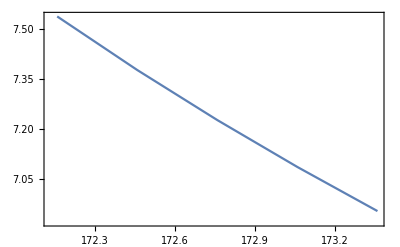

```mathematica
ListLinePlot[tabSMvp]
```

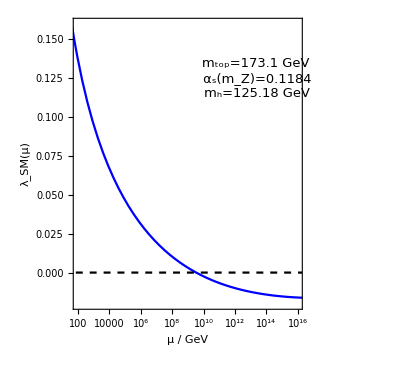

```mathematica
p0=LogLinearPlot[{{λ[Log[x/mZ]]},0},{x,10,10^17},
PlotRange->{{100,10^16},{-0.02,0.16}},
PlotStyle->{Blue,Directive[Black,Dashed]},
AspectRatio->0.9,
Frame-> {{True,True},{True,True}},FrameStyle->Directive[15,Black],
FrameTicksStyle->15,
FrameTicks->{{Automatic,None},{{{10^2,"10^2",{0.02,0.}},{10^5,"10^5",{0.02,0.}},{10^8,"10^8",{0.02,0.}},{10^11,"10^11",{0.02,0.}},{10^14,"10^14",{0.02,0.}}},None}},
PlotRange->{Full,Full},
FrameLabel->  {"μ / GeV","λ_SM(μ)"},
Epilog->{
Inset[Style[Rotate["m_top=173.1 GeV\n α_s(m_Z)=0.1184\n m_h=125.18 GeV",0Degree],FontSize->13],{Log[10^13.3],0.125}]
}
]
```